Autor: Artur Bednarczyk

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 10

Metoda odchyłek ważonych

Napisać procedurę realizującą metodę odchyłek ważonych dla równania:

u''(x)-u'(x)=0,   x∈(0,1),

z warunkami brzegowymi:

u(0)=1,
u'(1)=2.

Funkcje kształtu nie muszą zapewniać spełnienia warunków brzegowych.

a) Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone przyjmując jako funkcje kształtu:

Φ_1(x)=1,   
Φ_2(x)=x,   
Φ_3(x)=x^2,  

a jako funkcje wagowe:

w_1(x)=1,   
w_2(x)=x,   
w_3(x)=x^2.

Jako funkcje wagowe na brzegu przyjąć funkcje w_i.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym (wynik podać w postaci ułamka dziesiętnego).

b) Wykonać te same obliczenia dla funkcji kształtu postaci:

Φ_1(x)=1,   
Φ_2(x)=exp x .   

Jako funkcje wagowe przyjąć pierwsze dwie funkcje wagowe z poprzedniego zadania.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym.

## Rozwiązanie

```mathematica
ClearAll["Global`*"];
(* Metoda Odchyłek Ważonych *)
mow1[a_,b_]:=Module[{
f1 =1,
f2 =x,
f3=x^2,
result,T, r,e,res
},

T = Table[0,{i,1,3}];
e = Table[0, {i,1,3}];

T⟦1⟧ = p1*f1+p2*f2+p3*f3;
T⟦2⟧ = D[T⟦1⟧,x];
T⟦3⟧ = D[T⟦2⟧, x];

r0 =T⟦3⟧-T⟦2⟧;
r1  =T⟦1⟧-1;
r2 = T⟦2⟧-2;

e⟦1⟧ =∫_a^b f1*r0ⅆx+(f1*r1/.{x->a})+(f1*r2/.{x->b}) == 0;
e⟦2⟧ =∫_a^b f2*r0ⅆx+(f2*r1/.{x->a})+(f2*r2/.{x->b}) == 0;
e⟦3⟧ =∫_a^b f3*r0ⅆx+(f3*r1/.{x->a})+(f3*r2/.{x->b}) == 0;
result = Solve[e];
res = T⟦1⟧ /.{p1->result⟦1,1,2⟧, p2->result⟦1,2,2⟧, p3->result⟦1,3,2⟧};
Return[Simplify[res]];
];
mow2[a_,b_]:=Module[{
f1 =1,
f2 =Exp[x],
result,T, r,e,res
},

T = Table[0,{i,1,3}];
e = Table[0, {i,1,2}];

T⟦1⟧ = p1*f1+p2*f2;
T⟦2⟧ = D[T⟦1⟧,x];
T⟦3⟧ = D[T⟦2⟧, x];

r0 =T⟦3⟧-T⟦2⟧;
r1  =T⟦1⟧-1;
r2 = T⟦2⟧-2;

e⟦1⟧ =∫_a^b f1*r0ⅆx+(f1*r1/.{x->a})+(f1*r2/.{x->b}) == 0;
e⟦2⟧ =∫_a^b f2*r0ⅆx+(f2*r1/.{x->a})+(f2*r2/.{x->b}) == 0;
result = Solve[e];
res = T⟦1⟧ /.{p1->result⟦1,1,2⟧, p2->result⟦1,2,2⟧};
Return[Simplify[res]];
];
```

Rozwiązanie przybliżone: 3/17 (5+4 x+4 x^2)

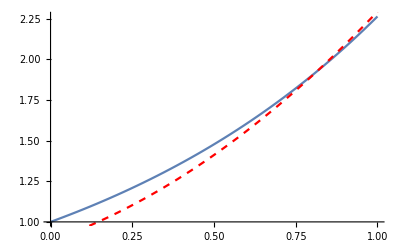

Norma L2: 0.00576518

Rozwiązanie przybliżone: (-2+ⅇ+2 ⅇ^x)/ⅇ

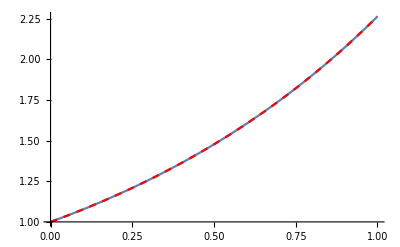

Norma L2: 0.

```mathematica
(* Dane *)
a = 0;
b = 1;
(* Rozwiązanie dokładne *)
r = DSolveValue[{u''[x]-u'[x]==0, u'[1] == 2,u[0]==1}, u[x],x];
rPlot = Plot[r, {x,a,b}];
(* Przykład A *)
ra = mow1[a,b];
raPlot = Plot[ra, {x,a,b}, PlotStyle->{Red, Dashed}];
Print["Rozwiązanie przybliżone: ", ra];
Show[rPlot, raPlot]
raNormL2 = ∫_a^b (ra-r)^2 ⅆx;
Print["Norma L2: ", N[raNormL2]];

(* Przykład B *)
rb = mow2[a,b];
rbPlot = Plot[rb, {x,a,b}, PlotStyle->{Red, Dashed}];
Print["Rozwiązanie przybliżone: ", rb];
Show[rPlot, rbPlot]
rbNormL2 = ∫_a^b (rb-r)^2 ⅆx;
Print["Norma L2: ", N[rbNormL2]];
```